## Load data so we can get tid string

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

Options

```mathematica
fName="20181127-orb_1607-densPA_30-Mathematica.csv"
```

20181127-orb_1607-densPA_30-Mathematica.csv

```mathematica
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
Options[loadJVCSV]={printFName->False};
loadJVCSV[OptionsPattern[]]:=Module[{},
If[OptionValue[printFName],Print[fName]];(*
data=Cases[Import[inDir<>fName,"Table"],{_?NumberQ,___}];
data=Cases[Import[inDir<>fName,"Table"],{_?StringQ,___}]*)
data=Import[inDir<>fName,{"CSV","Data"},"HeaderLines"-> 1]
]
```

Header line

```mathematica
Import[inDir<>fName,{"Data",1,All}]//TableForm[#,TableDirections->Row]&
```

Tid | pot | potErr | cur | curErr | je | jeerr | nDown | nDownErr | downEpot | downEpotErr

Load variables

```mathematica
data=loadJVCSV[];
```

```mathematica
{tids,pots,potErrs,curs,curErrs,jes,jeErrs,dens,densErrs,densPots,densPotErrs}=data[[All,#]]&/@Range[1,11];
```

### Select times/indices

```mathematica
interval=2;
```

```mathematica
itvlTidStr=Switch[interval,
1,
{{"12:00:28.5","12:00:38.7"},{"12:00:40.0","12:00:48"}},
2,
{"01:04:28.5","01:04:41"} ;
Switch[fName,
"20180817-orb_1607-densPA_45-sRate0_63-Mathematica.csv",
{"01:04:29.3","01:04:40.5"},
"20180817-orb_1607-densPA_45-sRate1_89-Mathematica.csv",
{"01:04:29.3","01:04:41.5"},
"20180817-orb_1607-densPA_45-sRate0_31-Mathematica.csv",
{"01:04:29.3","01:04:41.5"},
"20181127-orb_1607-densPA_30-Mathematica.csv",
{"01:04:31.2","01:04:40.5"}]
];
```

```mathematica
itvlBounds=Switch[Length@Dimensions[itvlTidStr],
1,
Flatten@((minTidInd[#,tids])&/@itvlTidStr),
2,

{Flatten@((minTidInd[#,tids])&/@itvlTidStr[[1,;;]]),Flatten@((minTidInd[#,tids])&/@itvlTidStr[[2,;;]])}
];
```

```mathematica
tids[[#]]&/@itvlBounds
```

{01:04:31.219,01:04:40.055}

```mathematica
inds1=Switch[Length@Dimensions[itvlTidStr],
1,
Range@@itvlBounds,
2,
Flatten[{Range@@itvlBounds[[1,;;]],Range@@itvlBounds[[2,;;]]}]
];
```

```mathematica
tid=tids[[inds1]];
```

## Load other things

```mathematica
MVStr="nVJVJeV";
```

```mathematica
MVStr="JV";
```

```mathematica
SetDirectory["/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20181128/"]
```

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20181128

```mathematica
kFiles=FileNames[RegularExpression["Orb1607_itvl2_kappa-fixT74eV.*"<>MVStr<>"(-\\d\\d)?(_THELONIOUS)?.wdx"]]
```

{Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-01_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-01.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-02_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-02.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-03_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-03.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-04_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-05_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-06_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-07_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-08_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-09_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-10_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-11_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-12_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV_THELONIOUS.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV.wdx,Orb1607_itvl2_kappa-fixT74eV_nRolls300_nVJVJeV_THELONIOUS.wdx}

```mathematica
Length@kFiles
```

18

If you want the version showing what we got from simulations with fixT=90 eV for the Maxwellian fits, check THIS out

```mathematica
OLDMAXWELL=False;
```

```mathematica
gFiles=If[OLDMAXWELL,{"Orb1607_itvl2_Maxwell-fixT65eV_nRolls2000_nVJVJeV_ALD.wdx"},FileNames[RegularExpression["Orb1607_itvl2_Maxwell-fixT65eV.*"<>MVStr<>"(-\\d\\d)?.wdx"]]]
```

{Orb1607_itvl2_Maxwell-fixT65eV_nRolls2000_nVJVJeV.wdx}

RESTORE DATA FILES

```mathematica
For[i=1,i≤ Length@kFiles,i++,
Print[kFiles[[i]]];
If[FileExistsQ[kFiles[[i]]],
Print[Ja];
<<(kFiles[[i]]);
If[i==1,
kMCValsMaster=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};,
kMCVals=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
kMCValsMaster = Transpose[(Transpose[kMCValsMaster]~Join~Transpose[kMCVals])];
];
];
]
```

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-01_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-01.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-02_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-02.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-03_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-03.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-04_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-05_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-06_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-07_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-08_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-09_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-10_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-11_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV-12_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV_THELONIOUS.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls100_nVJVJeV.wdx

Ja

Orb1607_itvl2_kappa-fixT74eV_nRolls300_nVJVJeV_THELONIOUS.wdx

Ja

```mathematica
For[i=1,i≤ Length@gFiles,i++,
Print[gFiles[[i]]];
If[FileExistsQ[gFiles[[i]]],
Print[Ja];
<<(gFiles[[i]]);
If[i==1,
gMCValsMaster=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};,
gMCVals=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
gMCValsMaster = Transpose[(Transpose[gMCValsMaster]~Join~Transpose[gMCVals])];
];
];
]
```

Orb1607_itvl2_Maxwell-fixT65eV_nRolls2000_nVJVJeV.wdx

Ja

```mathematica
kMCValsMaster//Dimensions
```

{4,2000}

```mathematica
gMCValsMaster//Dimensions
```

{4,2000}

```mathematica
nKKeep = 2000;
nGKeep = 2000;
```

```mathematica
nKKeep = 6000;
nGKeep = 6000;
```

```mathematica
kMCValsSub = kMCValsMaster[[;;,1;;nKKeep]];
```

```mathematica
kMCValsSub//Dimensions
```

{4,2000}

```mathematica
gMCValsSub = gMCValsMaster[[;;,1;;nGKeep]];
```

```mathematica
gMCValsSub//Dimensions
```

{4,2000}

```mathematica
nTrialsK=(kMCValsSub//Dimensions)[[2]];
nTrialsG=(gMCValsSub//Dimensions)[[2]];
```

```mathematica
kMCVals=kMCValsSub;
gMCVals=gMCValsSub;
Clear[kMCValsMaster,gMCValsMaster,kMCValsSub,gMCValsSub];
```

Fickit

```mathematica
Flipped = False;
```

```mathematica
If [!Flipped,kMCVals[[4,;;]]=1.5/kMCVals[[4,;;]];Flipped=True;]
```

```mathematica
UseLog10RB = False;
```

## Plots!

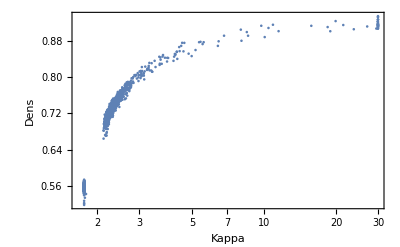

```mathematica
ListLogLinearPlot[Partition[Riffle[kMCVals[[4,;;]],kMCVals[[1,;;]]],2],Frame->True,FrameLabel->{"Kappa","Dens"}]
```

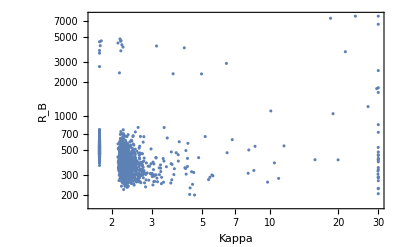

```mathematica
ListLogLogPlot[Partition[Riffle[kMCVals[[4,;;]],kMCVals[[3,;;]]],2],Frame->True,FrameLabel->{"Kappa","R_B"}]
```

```mathematica
kMCTitles={"N (cm^-3)","T (eV)","Log_10R_B","κ"};
kMCPDFTitles={"PDF (cm^3)","PDF (eV^-1)","PDF (R_B^-1)","PDF (κ^-1)"};
gMCTitles={"N (cm^-3)","T (eV)","R_B"};
```

```mathematica
binSizes=Table[Automatic,4];
```

```mathematica
binSizes={{0.005},{0.2},{100},{0.2}};
```

```mathematica
MCTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

```mathematica
densPlotRange:={{2.0,4.0},{0.48,0.94}};
```

```mathematica
If[MVStr=="JV",densPlotRange={{1.0,4.0},{0.4,1.2}};]
```

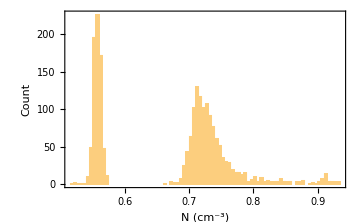
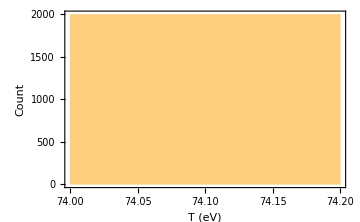
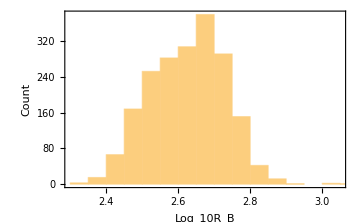
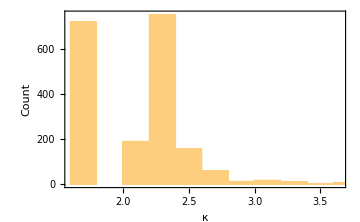

```mathematica
kHistosPlot=Row[Table[Histogram[If[MCParmInd==3,Log10[kMCVals[[MCParmInd]]],kMCVals[[MCParmInd]]],If[MCParmInd==3,Automatic,binSizes[[MCParmInd]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

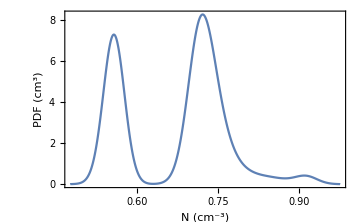
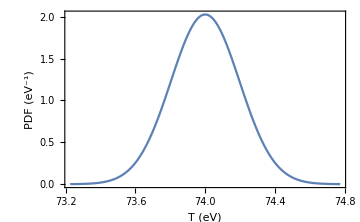
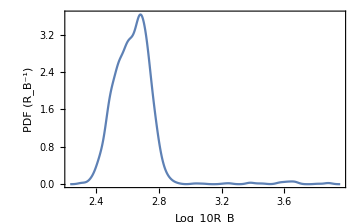
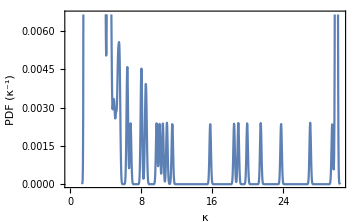

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[If[MCParmInd≠ 3,kMCVals[[MCParmInd]],Log10[kMCVals[[MCParmInd]]]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

```mathematica
n53to58LumpInds=Flatten@Position[kMCVals[[1]],_?(0.53≤ #≤0.58&)];
```

```mathematica
n66to9LumpInds=Flatten@Position[kMCVals[[1]],_?(0.66≤ #≤0.9&)];
```

```mathematica
RBLT31LumpInds=Flatten@Position[kMCVals[[3]],_?(Log10[#]≤3.1&)];
```

```mathematica
RBGT35LumpInds=Flatten@Position[kMCVals[[3]],_?(Log10[#]≥3.5&)];
```

For J-V, JE-V, n-V

```mathematica
n66to8LumpInds=Flatten@Position[kMCVals[[1]],_?(0.66≤ #≤0.8&)];
```

```mathematica
n52to6LumpInds=Flatten@Position[kMCVals[[1]],_?(0.52≤ #≤0.6&)];
```

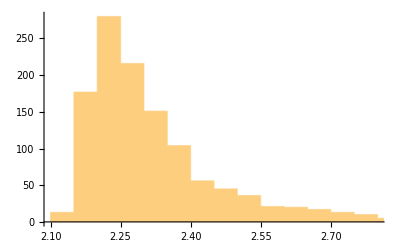

```mathematica
Histogram[(kMCVals[[4]])[[n66to8LumpInds]]]
```

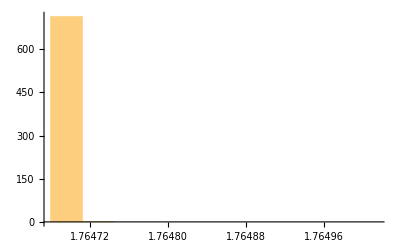

```mathematica
Histogram[(kMCVals[[4]])[[n52to6LumpInds]]]
```

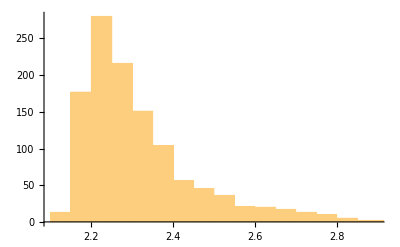

```mathematica
Histogram[(kMCVals[[4]])[[n66to9LumpInds]]]
```

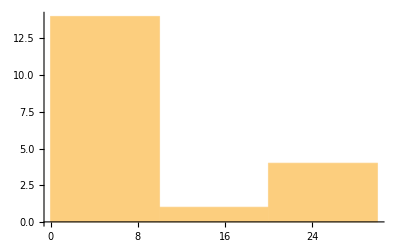

```mathematica
Histogram[(kMCVals[[4]])[[RBGT35LumpInds]]]
```

## Nye vei, med RE axis

```mathematica
axVals={{3.16,1.53}, {10,2.19}, {31.6,3.17}, {100,4.56}, {316,6.55}, {1000,9.66}, {3162,14.26}, {10000,15.66}, {20000,15.67}};
```

```mathematica
xVals=Round[Log10[axVals[[;;,1]]]*10]/10.//N;
```

```mathematica
log10XwithY=Partition[Riffle[xVals,axVals[[;;,2]]],2];
```

```mathematica
this=Interpolation[log10XwithY]
```

InterpolatingFunction[…]

```mathematica
(*RBVals={1.4,1.6,1.8,2.0};*)
```

```mathematica
this[2.6]
```

7.07056

```mathematica
RBVals={2.0,2.5,3.0,3.5,4.0};
```

```mathematica
REVals=this[RBVals]
```

{4.56,6.55,9.66,14.26,15.66}

```mathematica
REValsRound=Round[REVals*10]/10.
```

{4.6,6.6,9.7,14.3,15.7}

```mathematica
tics=Line[{{#,0.4+0.005},{#,0.4-0.005}}&/@RBVals]
```

Line[{{{2.,0.405},{2.,0.395}},{{2.5,0.405},{2.5,0.395}},{{3.,0.405},{3.,0.395}},{{3.5,0.405},{3.5,0.395}},{{4.,0.405},{4.,0.395}}}]

```mathematica
text=Text[#[[2]],{#[[1]],0.35}]&/@Partition[Riffle[RBVals,REValsRound],2]
```

{Text[4.6,{2.,0.35}],Text[6.6,{2.5,0.35}],Text[9.7,{3.,0.35}],Text[14.3,{3.5,0.35}],Text[15.7,{4.,0.35}]}

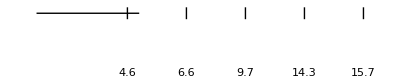

```mathematica
axis=Graphics[{Line[{{1.23,0.4},{2.1,0.4}}],tics,text}]
```

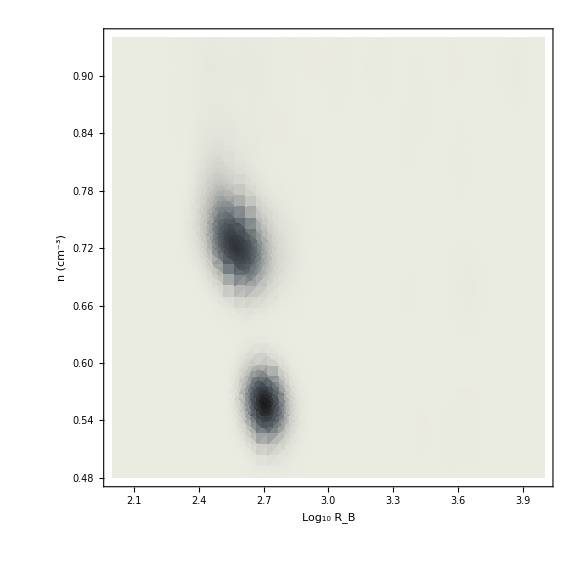

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrialsK],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}],PlotRangeClipping->False]
```

Maxwellian plots

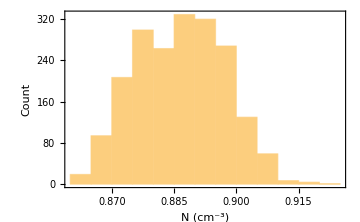
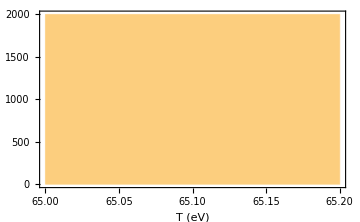
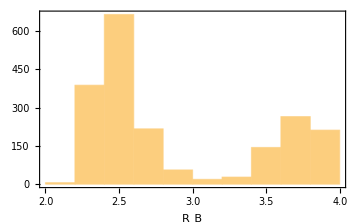

```mathematica
Row[Table[Histogram[If[MCParmInd≠ 3,gMCVals[[MCParmInd]],Log10[gMCVals[[MCParmInd]]]],If[MCParmInd≠ 3,binSizes[[MCParmInd]],Automatic],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

```mathematica
mWellTitle=ToString@StringForm["`1` (Maxwell, N = `2`)",MCTitle,nTrialsG];
```

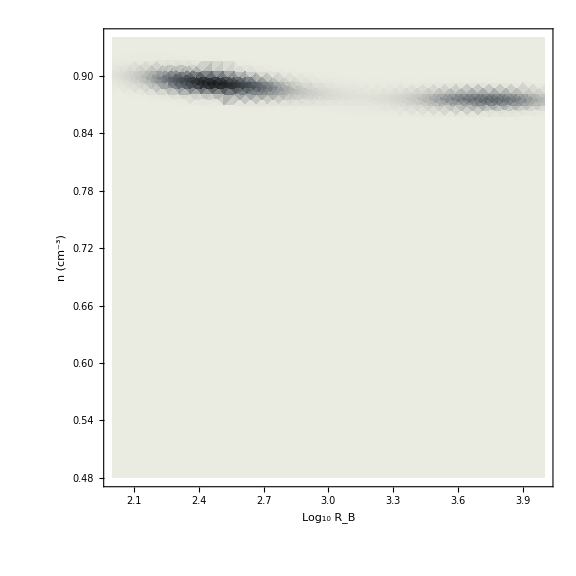

```mathematica
SmoothDensityHistogram[Partition[Riffle[Log10[gMCVals[[3]]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[mWellTitle,Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

## Gammel vei, uten RE axis

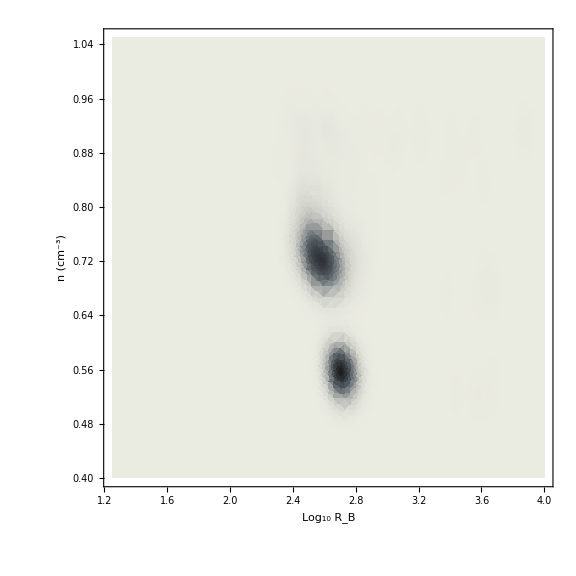

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrialsK],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

Maxwellian plots

```mathematica
Row[Table[Histogram[If[MCParmInd≠ 3,gMCVals[[MCParmInd]],Log10[gMCVals[[MCParmInd]]]],If[MCParmInd≠ 3,binSizes[[MCParmInd]],Automatic],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

-Graphics--Graphics--Graphics-

```mathematica
(*mWellTitle=If[checkout90eVMaxwellianFiles,ToString@StringForm["`1` (Mwell, N=`2`, fixT=`3`eV)",MCTitle,nTrialsG,90],ToString@StringForm["`1` (Maxwell, N = `2`)",MCTitle,nTrialsG]];*)
```

```mathematica
mWellTitle=ToString@StringForm["`1` (Maxwell, N = `2`)",MCTitle,nTrialsG];
```

```mathematica
SmoothDensityHistogram[Partition[Riffle[Log10[gMCVals[[3]]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[mWellTitle,Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

-Graphics-

## STATS

### Kappa stats

```mathematica
kLT2Inds=Flatten@Position[kMCVals[[4]],_?(#<2&)];
```

```mathematica
kGE2Inds=Flatten@Position[kMCVals[[4]],_?(#≥2&)];
```

```mathematica
kGE2LE5Inds=Flatten@Position[kMCVals[[4]],_?(2≤#≤5&)];
```

```mathematica
kGE2LE10Inds=Flatten@Position[kMCVals[[4]],_?(2≤#≤10&)];
```

```mathematica
kGE2LE35Inds=Flatten@Position[kMCVals[[4]],_?(2≤#≤35&)];
```

```mathematica
useHistoInds=kLT2Inds;
```

```mathematica
useHistoInds=kGE2Inds;
```

```mathematica
useHistoInds=kGE2LE5Inds;
```

```mathematica
useHistoInds=kGE2LE35Inds;
```

#### k ALL

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[Log10[kMCVals[[3]]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrialsK],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}],PlotRangeClipping->False]
```

-Graphics-

#### k GE 2 inds

```mathematica
useHistoInds=kGE2Inds;
```

```mathematica
{{"","LOG10RB",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(Log10[kMCVals[[3]]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[Log10[kMCVals[[3]]],{0.1,0.9}]}//TableForm

{{"","RB",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[3]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[3]],{0.1,0.9}]}//TableForm

{{"","RE",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(this[Log10[kMCVals[[3]]]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[this[Log10[kMCVals[[3]]]],{0.1,0.9}]}//TableForm

{{"","DENSITY",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[1]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[1]],{0.1,0.9}]}//TableForm
```

| LOG10RB | 
Who | 1st decile | 9th decile
useHistoInds | 3.33038 | 3.99995
All | 2.89474 | 3.99994

| RB | 
Who | 1st decile | 9th decile
useHistoInds | 2139.81 | 9998.78
All | 784.767 | 9998.72

| RE | 
Who | 1st decile | 9th decile
useHistoInds | 12.8235 | 15.66
All | 8.89387 | 15.66

| DENSITY | 
Who | 1st decile | 9th decile
useHistoInds | 0.682069 | 0.839038
All | 0.601826 | 0.830191

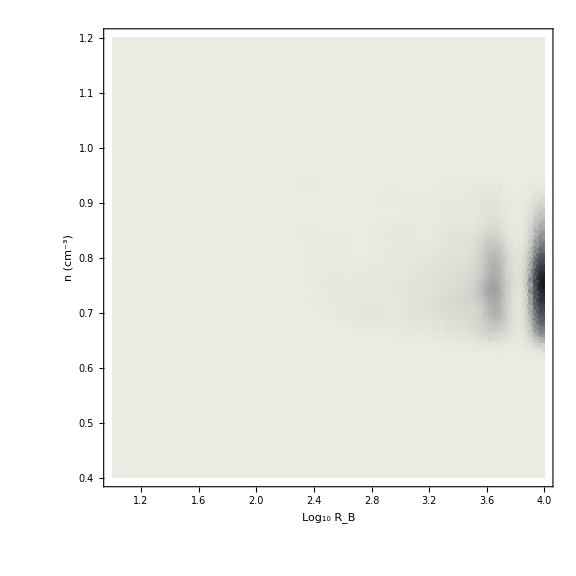

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[(Log10[kMCVals[[3]]])[[kGE2Inds]],(kMCVals[[1]])[[kGE2Inds]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[ToString@StringForm["`1` (Kappa GE 2, N = `2`)",MCTitle,nTrialsK],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}],PlotRangeClipping->False]
```

#### 10 GE k GE 2 inds

```mathematica
useHistoInds=kGE2LE10Inds;
```

```mathematica
{{"","LOG10RB",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(Log10[kMCVals[[3]]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[Log10[kMCVals[[3]]],{0.1,0.9}]}//TableForm

{{"","RB",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[3]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[3]],{0.1,0.9}]}//TableForm

{{"","RE",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(this[Log10[kMCVals[[3]]]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[this[Log10[kMCVals[[3]]]],{0.1,0.9}]}//TableForm

{{"","DENSITY",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[1]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[1]],{0.1,0.9}]}//TableForm
```

| LOG10RB | 
Who | 1st decile | 9th decile
useHistoInds | 2.47096 | 2.69835
All | 2.48743 | 2.7586

| RB | 
Who | 1st decile | 9th decile
useHistoInds | 295.773 | 499.286
All | 307.209 | 573.589

| RE | 
Who | 1st decile | 9th decile
useHistoInds | 6.4088 | 7.6291
All | 6.48844 | 7.9953

| DENSITY | 
Who | 1st decile | 9th decile
useHistoInds | 0.703118 | 0.776027
All | 0.55383 | 0.765032

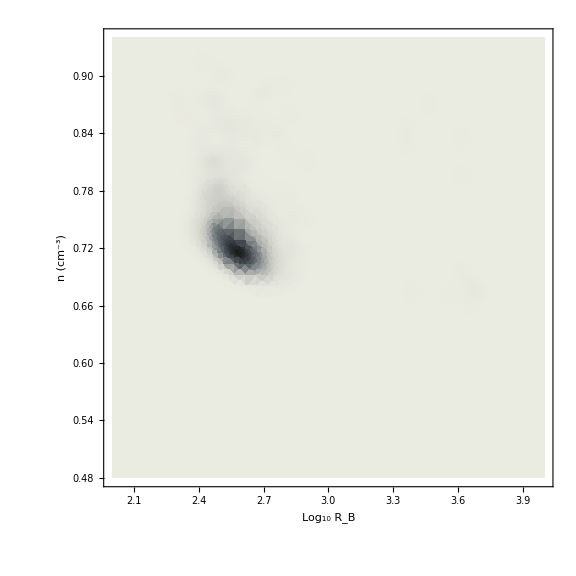

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[(Log10[kMCVals[[3]]])[[useHistoInds]],(kMCVals[[1]])[[useHistoInds]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[ToString@StringForm["`1` (2≤κ≤10, N = `2`)",MCTitle,Length[useHistoInds]],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}],PlotRangeClipping->False]
```

#### k LT 2 stats

```mathematica
useHistoInds=kLT2Inds;
```

```mathematica
{{"","LOG10RB",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(Log10[kMCVals[[3]]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[Log10[kMCVals[[3]]],{0.1,0.9}]}//TableForm

{{"","RB",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[3]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[3]],{0.1,0.9}]}//TableForm

{{"","RE",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(this[Log10[kMCVals[[3]]]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[this[Log10[kMCVals[[3]]]],{0.1,0.9}]}//TableForm

{{"","DENSITY",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[1]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[1]],{0.1,0.9}]}//TableForm
```

| LOG10RB | 
Who | 1st decile | 9th decile
useHistoInds | 2.64541 | 2.77893
All | 2.48743 | 2.7586

| RB | 
Who | 1st decile | 9th decile
useHistoInds | 441.992 | 601.079
All | 307.209 | 573.589

| RE | 
Who | 1st decile | 9th decile
useHistoInds | 7.32256 | 8.12313
All | 6.48844 | 7.9953

| DENSITY | 
Who | 1st decile | 9th decile
useHistoInds | 0.550178 | 0.564248
All | 0.55383 | 0.765032

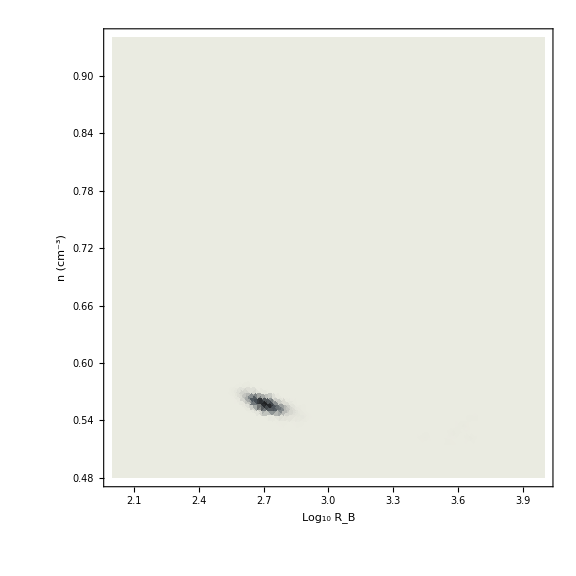

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[(Log10[kMCVals[[3]]])[[useHistoInds]],(kMCVals[[1]])[[useHistoInds]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->22, FrameLabel->{{"n (cm^-3)",""},{"Log_10 R_B",Style[ToString@StringForm["`1` (κ < 2, N = `2`)",MCTitle,Length[useHistoInds]],Bold,22]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}],PlotRangeClipping->False]
```

### Maxwellian stats

```mathematica
{{"","1st decile","9th decile"},
{"RB"}~Join~Quantile[gMCVals[[3]],{0.1,0.9}],
{"RE"}~Join~Quantile[this[Log10[gMCVals[[3]]]],{0.1,0.9}],
{"DENS"}~Join~Quantile[gMCVals[[1]],{0.1,0.9}]
}//TableForm
```

| 1st decile | 9th decile
RB | 218.727 | 6396.77
RE | 5.81582 | 15.3884
DENS | 0.872432 | 0.900001

```mathematica
gRBLT3p2Inds=Flatten@Position[Log10[gMCVals[[3]]],_?(#<3.2&)];
gRBGE3p2Inds=Flatten@Position[Log10[gMCVals[[3]]],_?(#≥3.2&)];
```

```mathematica
useHistoInds=gRBLT3p2Inds;
```

```mathematica
{{"","1st decile","9th decile"},
{"RB"}~Join~Quantile[(gMCVals[[3]])[[useHistoInds]],{0.1,0.9}],
{"RE"}~Join~Quantile[(this[Log10[gMCVals[[3]]]])[[useHistoInds]],{0.1,0.9}],
{"DENS"}~Join~Quantile[(gMCVals[[1]])[[useHistoInds]],{0.1,0.9}]
}//TableForm
```

| 1st decile | 9th decile
RB | 205.174 | 516.553
RE | 5.69886 | 7.71711
DENS | 0.881398 | 0.902062

```mathematica
useHistoInds=gRBGE3p2Inds;
```

```mathematica
{{"","1st decile","9th decile"},
{"RB"}~Join~Quantile[(gMCVals[[3]])[[useHistoInds]],{0.1,0.9}],
{"RE"}~Join~Quantile[(this[Log10[gMCVals[[3]]]])[[useHistoInds]],{0.1,0.9}],
{"DENS"}~Join~Quantile[(gMCVals[[1]])[[useHistoInds]],{0.1,0.9}]
}//TableForm
```

| 1st decile | 9th decile
RB | 3188.84 | 7488.04
RE | 14.2797 | 15.5162
DENS | 0.868383 | 0.882489

## Bonus stats

```mathematica
kLT188Inds=Flatten@Position[kMCVals[[4]],_?(#<1.88&)];
```

```mathematica
kGE188Inds=Flatten@Position[kMCVals[[4]],_?(#≥1.88&)];
```

```mathematica
useHistoInds=kLT188Inds;
```

```mathematica
{{"","LOG10RB",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(Log10[kMCVals[[3]]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[Log10[kMCVals[[3]]],{0.1,0.9}]}//TableForm

{{"","RB",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[3]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[3]],{0.1,0.9}]}//TableForm

{{"","RE",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(this[Log10[kMCVals[[3]]]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[this[Log10[kMCVals[[3]]]],{0.1,0.9}]}//TableForm

{{"","κ",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[4]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[4]],{0.1,0.9}]}//TableForm

{{"","DENSITY",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[1]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[1]],{0.1,0.9}]}//TableForm
```

| LOG10RB | 
Who | 1st decile | 9th decile
useHistoInds | 2.64541 | 2.77893
All | 2.48743 | 2.7586

| RB | 
Who | 1st decile | 9th decile
useHistoInds | 441.992 | 601.079
All | 307.209 | 573.589

| RE | 
Who | 1st decile | 9th decile
useHistoInds | 7.32256 | 8.12313
All | 6.48844 | 7.9953

| κ | 
Who | 1st decile | 9th decile
useHistoInds | 1.76471 | 1.76471
All | 1.76471 | 2.55197

| DENSITY | 
Who | 1st decile | 9th decile
useHistoInds | 0.550178 | 0.564248
All | 0.55383 | 0.765032

```mathematica
useHistoInds=kGE188Inds;
```

```mathematica
{{"","LOG10RB",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(Log10[kMCVals[[3]]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[Log10[kMCVals[[3]]],{0.1,0.9}]}//TableForm

{{"","RB",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[3]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[3]],{0.1,0.9}]}//TableForm

{{"","RE",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(this[Log10[kMCVals[[3]]]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[this[Log10[kMCVals[[3]]]],{0.1,0.9}]}//TableForm

{{"","κ",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[4]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[4]],{0.1,0.9}]}//TableForm

{{"","DENSITY",""},{"Who","1st decile","9th decile"},{"useHistoInds"}~Join~Quantile[(kMCVals[[1]])[[useHistoInds]],{0.1,0.9}],{"All"}~Join~Quantile[kMCVals[[1]],{0.1,0.9}]}//TableForm
```

| LOG10RB | 
Who | 1st decile | 9th decile
useHistoInds | 2.47012 | 2.70724
All | 2.48743 | 2.7586

| RB | 
Who | 1st decile | 9th decile
useHistoInds | 295.203 | 509.607
All | 307.209 | 573.589

| RE | 
Who | 1st decile | 9th decile
useHistoInds | 6.40478 | 7.68193
All | 6.48844 | 7.9953

| κ | 
Who | 1st decile | 9th decile
useHistoInds | 2.18753 | 2.76333
All | 1.76471 | 2.55197

| DENSITY | 
Who | 1st decile | 9th decile
useHistoInds | 0.703293 | 0.787231
All | 0.55383 | 0.765032